```mathematica
(*Used for generating sphere packings shown in Fig. 1(a). Takes <1 minute to run.*)
centers={};
i=1;
```

```mathematica
(*Tries to place points completely at random so that they are within the square [0,1.1]x[0,1.1]. For each point, it makes sure the centers are placed at least 0.1 away from every other center. It attempts to place points 75000 times.*)
While[i≤ 75000,
{xtry,ytry}=1.1*{RandomReal[],RandomReal[]};
dists={};
k=1;
While[k≤ Length[centers],
dists=Append[dists,Norm[{xtry,ytry}-centers[[k]]]];
k++;];
checklist=3*ConstantArray[0.033,Length[dists]];
If[Reduce[dists≥ checklist],centers=Append[centers,{xtry,ytry}]];
i++;]
```

```mathematica
(*Now it draws circles of radius 0.075 at each center location. Note that circles will overlap because the points were only required to be 0.1 away from each other, and 0.1<2*0.075=0.15.*)
j=1;
circles={};
While[j≤ Length[centers],
circles=Append[circles,Graphics[{EdgeForm[Thickness[0.012]],RGBColor[0.5,0.5,0.5,0.3],Disk[centers[[j]],3*0.025]}]];
j++;]
```

```mathematica
(*For every circle that touches, a red line is drawn between them to represent the disordered contact network.*)
q=1;
contactnetwork={};
While[q≤ Length[centers],
r=1;
While[r< q,
If[Norm[centers[[r]]-centers[[q]]]≤ 0.156,contactnetwork=Append[contactnetwork,Graphics[{Red,Thickness[0.01],Line[{centers[[r]],centers[[q]]}]}]]];
r++;];
q++;]
```

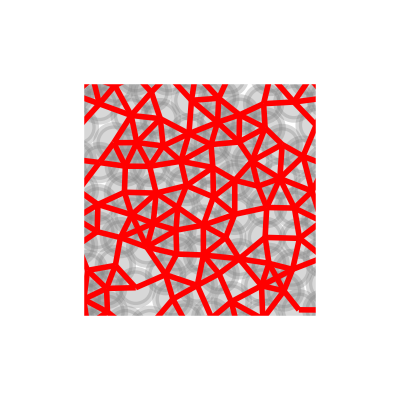

```mathematica
(*The figure is drawn. I export this into InkScape and appropriately crop it for import into PlasmonPictures to be the high density part of Fig. 1(a).*)
BorderRect=Graphics[{{White,Rectangle[{-0.156,-0.156},{0.05,1.256}]},{White,Rectangle[{1.05,-0.156},{1.256,1.256}]},{White,Rectangle[{-0.156,-0.156},{1.256,0.05}]},{White,Rectangle[{-0.156,1.05},{1.256,1.256}]}}];
Show[{circles,contactnetwork,BorderRect},AspectRatio->1]
```

```mathematica
(*Checking the isostaticity condition. If the coordination number is >2d=4, the network is (on average) rigid in the thermodynamic limit.*)
N[(2*Length[contactnetwork])/Length[centers]]
```

4.35789

```mathematica
(*The rest of the code is identical to the one above, but when placing the points, the centers are required to be 0.123 apart. The spheres can still touch, because 0.123<2*0.075=0.15, but it becomes less likely, and we get a lower-density sphere packing.*)
centers={};
i=1;
```

```mathematica
While[i≤ 75000,
{xtry,ytry}=1.1*{RandomReal[],RandomReal[]};
dists={};
k=1;
While[k≤ Length[centers],
dists=Append[dists,Norm[{xtry,ytry}-centers[[k]]]];
k++;];
checklist=3*ConstantArray[0.041,Length[dists]];
If[Reduce[dists≥ checklist],centers=Append[centers,{xtry,ytry}]];
i++;]
```

```mathematica
j=1;
circles={};
While[j≤ Length[centers],
circles=Append[circles,Graphics[{EdgeForm[Thickness[0.012]],RGBColor[0.5,0.5,0.5,0.3],Disk[centers[[j]],3*0.025]}]];
j++;]
```

```mathematica
q=1;
contactnetwork={};
While[q≤ Length[centers],
r=1;
While[r< q,
If[Norm[centers[[r]]-centers[[q]]]≤ 0.156,contactnetwork=Append[contactnetwork,Graphics[{Red,Thickness[0.01],Line[{centers[[r]],centers[[q]]}]}]]];
r++;];
q++;]
```

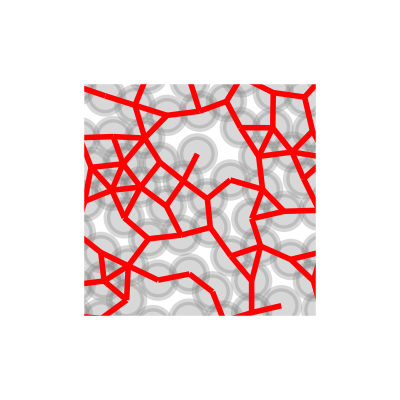

```mathematica
BorderRect=Graphics[{{White,Rectangle[{-0.156,-0.156},{0.05,1.256}]},{White,Rectangle[{1.05,-0.156},{1.256,1.256}]},{White,Rectangle[{-0.156,-0.156},{1.256,0.05}]},{White,Rectangle[{-0.156,1.05},{1.256,1.256}]}}];
Show[{circles,contactnetwork,BorderRect},AspectRatio->1]
```

```mathematica
(*Checking the isostaticity condition should give an average coordination number <2d=4, indicating this structure is (on average) floppy in the thermodynamic limit.*)
N[(2*Length[contactnetwork])/Length[centers]]
```

2.8125